# Drawing Figure 2

## Equations of the corner and internal equilibria

```mathematica
x1Eq=1-(μ β + μ(β-γ))(1+β)/(β(β-γ))/.{β->b f/4,γ->b c/8};
x4Eq=μ μ ((1+β)(2β-γ+δ+β(β+δ)))/(β(β-γ)(β+δ))/.{β->b f/4,γ->b c/8,δ->b(c/2+(1-c)r)/8+r(1-b/2)(1-f)/4};
xIntEq=0.25+DD/.DD->(2δ+4μ(1-δ)-Sqrt[R])/(4(γ-β)-8μ(β+γ))/.R->4(δ+2μ(1-δ))^2+γ^2(1-2μ)^2-2β γ(1-2μ)+β^2(1-4μ^2)/.{β->b f/4,γ->b c/8,δ->b(c/2+(1-c)r)/8+r(1-b/2)(1-f)/4};
```

## Importing the results from the numerical simulations

```mathematica
BasinCycC1Mu0000000000001=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Mutation Model\\Basin_of_attraction\\AttractionBasinWithMutMAC\\Data_Basin_of_attraction\\outputCycMut_c1_mu = 1e-12.dat","Table"];
BasinCycC1Mu0000001=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Mutation Model\\Basin_of_attraction\\AttractionBasinWithMutMAC\\Data_Basin_of_attraction\\\outputCycMut_c1_mu = 1e-06.dat","Table"];
BasinCycC1Mu000001=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Mutation Model\\Basin_of_attraction\\AttractionBasinWithMutMAC\\Data_Basin_of_attraction\\\outputCycMut_c1_mu = 1e-05.dat","Table"];
BasinCycC1Mu000002=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Mutation Model\\Basin_of_attraction\\AttractionBasinWithMutMAC\\Data_Basin_of_attraction\\\outputCycMut_c1_mu = 2e-05.dat","Table"];
```

## Adapting the data to the graphical representation

```mathematica
Absc=Array[BasinCycC1Mu0000000000001[[1]][[1]]*#&,1];
For[i=1,i<Length[BasinCycC1Mu0000000000001],++i,
If[BasinCycC1Mu0000000000001[[i]][[1]]!=BasinCycC1Mu0000000000001[[i+1]][[1]],
Absc2=Array[BasinCycC1Mu0000000000001[[i+1]][[1]]*#&,1];
Absc=Join[Absc,Absc2];]]
SupC1Mu0000000000001=Array[0#&,{Length[Absc],2}];
InfC1Mu0000000000001=Array[0#&,{Length[Absc],2}];
For[j=1,j<Length[Absc]+1,++j,
InfC1Mu0000000000001[[j]][[1]]=Absc[[j]];
SupC1Mu0000000000001[[j]][[1]]=Absc[[j]];
For[k=1,k<Length[BasinCycC1Mu0000000000001],++k,
If[BasinCycC1Mu0000000000001[[k]][[1]]==Absc[[j]],
If[(BasinCycC1Mu0000000000001[[k]][[2]]<0.5)&&(BasinCycC1Mu0000000000001[[k+1]][[2]]>0.5),
InfC1Mu0000000000001[[j]][[2]]=BasinCycC1Mu0000000000001[[k]][[2]];
SupC1Mu0000000000001[[j]][[2]]=BasinCycC1Mu0000000000001[[k+1]][[2]];
]
]
]];
```

```mathematica
Absc=Array[BasinCycC1Mu0000001[[1]][[1]]*#&,1];
For[i=1,i<Length[BasinCycC1Mu0000001],++i,
If[BasinCycC1Mu0000001[[i]][[1]]!=BasinCycC1Mu0000001[[i+1]][[1]],
Absc2=Array[BasinCycC1Mu0000001[[i+1]][[1]]*#&,1];
Absc=Join[Absc,Absc2];]]
SupC1Mu0000001=Array[0#&,{Length[Absc],2}];
InfC1Mu0000001=Array[0#&,{Length[Absc],2}];
For[j=1,j<Length[Absc]+1,++j,
InfC1Mu0000001[[j]][[1]]=Absc[[j]];
SupC1Mu0000001[[j]][[1]]=Absc[[j]];
For[k=1,k<Length[BasinCycC1Mu0000001],++k,
If[BasinCycC1Mu0000001[[k]][[1]]==Absc[[j]],
If[(BasinCycC1Mu0000001[[k]][[2]]<0.5)&&(BasinCycC1Mu0000001[[k+1]][[2]]>0.5),
InfC1Mu0000001[[j]][[2]]=BasinCycC1Mu0000001[[k]][[2]];
SupC1Mu0000001[[j]][[2]]=BasinCycC1Mu0000001[[k+1]][[2]];
]
]
]];
```

```mathematica
Absc=Array[BasinCycC1Mu000001[[1]][[1]]*#&,1];
For[i=1,i<Length[BasinCycC1Mu000001],++i,
If[BasinCycC1Mu000001[[i]][[1]]!=BasinCycC1Mu000001[[i+1]][[1]],
Absc2=Array[BasinCycC1Mu000001[[i+1]][[1]]*#&,1];
Absc=Join[Absc,Absc2];]]
SupC1Mu000001=Array[0#&,{Length[Absc],2}];
InfC1Mu000001=Array[0#&,{Length[Absc],2}];
For[j=1,j<Length[Absc]+1,++j,
InfC1Mu000001[[j]][[1]]=Absc[[j]];
SupC1Mu000001[[j]][[1]]=Absc[[j]];
For[k=1,k<Length[BasinCycC1Mu000001],++k,
If[BasinCycC1Mu000001[[k]][[1]]==Absc[[j]],
If[(BasinCycC1Mu000001[[k]][[2]]<0.5)&&(BasinCycC1Mu000001[[k+1]][[2]]>0.5),
InfC1Mu000001[[j]][[2]]=BasinCycC1Mu000001[[k]][[2]];
SupC1Mu000001[[j]][[2]]=BasinCycC1Mu000001[[k+1]][[2]];
]
]
]];
```

```mathematica
Absc=Array[BasinCycC1Mu000002[[1]][[1]]*#&,1];
For[i=1,i<Length[BasinCycC1Mu000002],++i,
If[BasinCycC1Mu000002[[i]][[1]]!=BasinCycC1Mu000002[[i+1]][[1]],
Absc2=Array[BasinCycC1Mu000002[[i+1]][[1]]*#&,1];
Absc=Join[Absc,Absc2];]]
SupC1Mu000002=Array[0#&,{Length[Absc],2}];
InfC1Mu000002=Array[0#&,{Length[Absc],2}];
For[j=1,j<Length[Absc]+1,++j,
InfC1Mu000002[[j]][[1]]=Absc[[j]];
SupC1Mu000002[[j]][[1]]=Absc[[j]];
For[k=1,k<Length[BasinCycC1Mu000002],++k,
If[BasinCycC1Mu000002[[k]][[1]]==Absc[[j]],
If[(BasinCycC1Mu000002[[k]][[2]]<0.5)&&(BasinCycC1Mu000002[[k+1]][[2]]>0.5),
InfC1Mu000002[[j]][[2]]=BasinCycC1Mu000002[[k]][[2]];
SupC1Mu000002[[j]][[2]]=BasinCycC1Mu000002[[k+1]][[2]];
]
]
]];
```

## The Figure

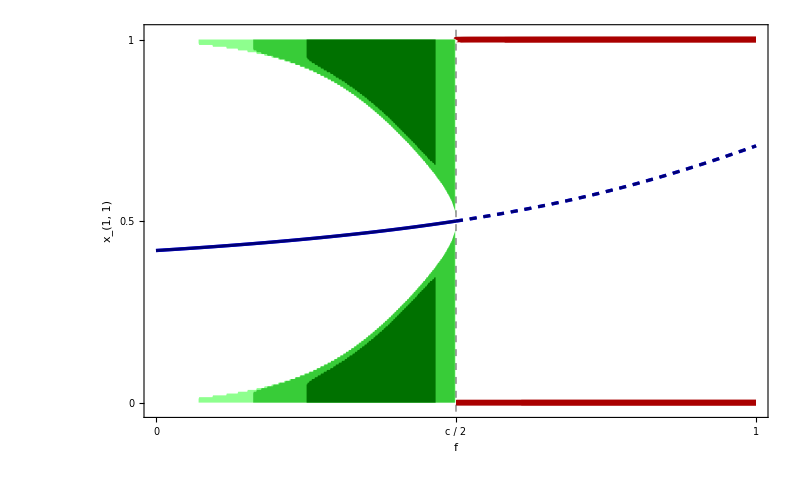

```mathematica
InfPlot=ListLinePlot[{InfC1Mu0000000000001,InfC1Mu0000001,InfC1Mu000002},PlotRange->{{0,1},{-0.02,1.02}},Filling->{1->{0,Lighter[Lighter[Green]]},2->{0,Directive[Darker[Green],Opacity[0.6]]},3->{0,Darker[Darker[Green]]}},Frame->True,PlotStyle->Directive[White,Opacity[0]],FrameTicks->{{{0,0.5,1},None},{{0,{0.5,"c / 2"},1},None}},FrameStyle->Directive[Black,Thick],FrameLabel->{Style["f",22],Style["x_(1, 1)",22]},RotateLabel->False,FrameTicksStyle->Directive[Black,Bold,16,Opacity[1],FontOpacity->1],FrameStyle->Directive[Bold,Black,18],GridLines->{{0.5},None},GridLinesStyle->Directive[Black,Dashed],ImageSize->{800,600}];
SupPlot=ListLinePlot[{SupC1Mu0000000000001,SupC1Mu0000001,SupC1Mu000002},PlotRange->{{0,1},{0,1}},Filling->{1->{Top,Lighter[Lighter[Green]]},2->{Top,Directive[Darker[Green],Opacity[0.6]]},3->{Top,Darker[Darker[Green]]}},PlotStyle->Directive[White,Opacity[0]]];
plotX1Eq=Plot[{x1Eq/.{b->1,c->1,r->1,μ->10^(-12)},x1Eq/.{b->1,c->1,r->1,μ->10^(-6)},x1Eq/.{b->1,c->1,r->1,μ->10^(-5)}},{f,0.5,1},PlotStyle->{Directive[Darker[Red],Thickness[0.005]],Directive[Darker[Red],Thickness[0.005]],Directive[Darker[Red],Thickness[0.005]]}];
plotX4Eq=Plot[{x4Eq/.{b->1,c->1,r->1,μ->10^(-12)},x4Eq/.{b->1,c->1,r->1,μ->10^(-6)},x4Eq/.{b->1,c->1,r->1,μ->10^(-5)}},{f,0.5,1},PlotStyle->{Directive[Darker[Red],Thickness[0.005]],Directive[Darker[Red],Thickness[0.005]],Directive[Darker[Red],Thickness[0.005]]}];
plotXIntEqInf=Plot[{2*xIntEq/.{b->1,c->1,r->1,μ->10^(-12)},2*xIntEq/.{b->1,c->1,r->1,μ->10^(-6)},2*xIntEq/.{b->1,c->1,r->1,μ->10^(-5)}},{f,0,0.5},PlotStyle->{Directive[Lighter[Blue],Thickness[0.003]],Directive[Darker[Blue],Thickness[0.003]],Directive[Darker[Darker[Blue]],Thickness[0.002]]}];
plotXIntEqSup=Plot[{2*xIntEq/.{b->1,c->1,r->1,μ->10^(-12)},2*xIntEq/.{b->1,c->1,r->1,μ->10^(-6)},2*xIntEq/.{b->1,c->1,r->1,μ->10^(-5)}},{f,0.5,1},PlotStyle->{Directive[Lighter[Blue],Thickness[0.003],Dashed],Directive[Darker[Blue],Thickness[0.003],Dashed],Directive[Darker[Darker[Blue]],Thickness[0.002],Dashed]}];
Figc10=Show[{InfPlot,SupPlot,plotX1Eq,plotX4Eq,plotXIntEqInf,plotXIntEqSup}]
```